# Computes WiFi intensity in a given configuration of walls and antenna.

laantoi

We reduce Maxwell equations via a series of approximations to the stationary Helmholtz equation, which we use to model the WiFi signal.

```mathematica
DateString[]
```

Sun 15 Oct 2017 19:19:54

```mathematica
ClearAll["Global`*"];Clear[Derivative];Remove["Global`*"];
```

```mathematica
$Assumptions={x,y}∈Reals&&{u}∈ Complexes;
```

```mathematica
Needs["NDSolve`FEM`"]
```

## Definitions

```mathematica
freq=2.4*10^9; (* WiFi frequency in Hz *)
λ:=299792458/freq; (* Wavelength in meters. For a 2.4 GHz signal, the wavelength is ≈ 12.5 cm*)
k:=2π/λ;(* k is the wavenumber*)
```

```mathematica
nair:=1.0; (*refractive index for air*)
nconcrete:=2.55-0.01ⅈ ;(*refractive index for concrete. The small imaginary part describes wave attenuation.*)
```

```mathematica
inside=Rectangle[{-4,-4},{4,4}];
walls=RegionDifference[Rectangle[{-5,-5},{5,5}],inside];
```

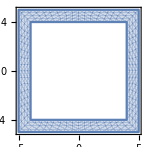

```mathematica
RegionPlot[walls]
```

```mathematica
n[x_,y_]:=  If[{x,y}∈ walls,nconcrete,nair]; (*Refractive index field*)
```

```mathematica
f[x_,y_]:= Piecewise[{{1.0,{x,y}∈ Disk[{3,3},0.2]},{1.0,{x,y}∈ Disk[{-3,-3},0.2]}}];(* Forcing term, i.e. the antenna. *)
```

Define the Helmholtz equation that we want to solve for the electric field u:

```mathematica
heqn={Laplacian[u[x,y],{x,y}]+(k/n[x,y])^2 u[x,y]==f[x,y]};
```

Boundary conditions

```mathematica
boxsize:=6.0;
Ω:=ImplicitRegion[-boxsize≤x≤boxsize &&-boxsize≤y≤boxsize ,{x,y}] ;
(*bc:=DirichletCondition[u[x,y]==0,True];*)
bc:={u[x,boxsize]==0,u[x,-boxsize]==0,u[boxsize,y]==0,u[-boxsize,y]==0};
```

Create the discretization grid. Note: the mesh must be accurate enough to capture features on the order of the radiation wavelength λ. We also make the grid follow the walls.

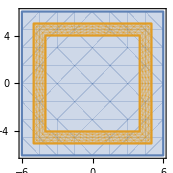

```mathematica
RegionPlot[{Ω,walls}]
```

```mathematica
(*This is otherwise fully general, but we must specify by hand one point inside each subregion (not necessary if we use the same grid spacing throughout). For more accurate evaluation we need grid points on the wall boundaries. Based on https://mathematica.stackexchange.com/questions/73914/join-two-element-meshes *)
ptinside:={0, 0.};
ptwalls:={-4.5, 0.};
ptoutside:={5.5, 0.};
maxcellmeasureinside:=0.0001 (* the maximum area a discretization cell can be. The smaller the better. *)
maxcellmeasurewalls:=0.0001(* the maximum area a discretization cell can be. The smaller the better. *)
maxcellmeasureoutside:=0.0001(* the maximum area a discretization cell can be. The smaller the better. *)
r=RegionPlot[{Ω,walls}];
bmesh=ToBoundaryMesh["Coordinates"->Round[#,0.001]&@First@Cases[r,GraphicsComplex[v_,___]:>v,∞],"BoundaryElements"->Cases[r,Line[p_,___]:>LineElement@Partition[p,2,1],∞]];
bmesh@"Wireframe";
mesh=ToElementMesh[bmesh,"RegionMarker"-> {{ptinside,0,maxcellmeasureinside},{ptwalls,1,maxcellmeasurewalls},{ptoutside,2,maxcellmeasureoutside}},"NodeReordering"->True];
mesh["Wireframe"];
```

We need grid points that can represent variations on the scale k*x.

```mathematica
(*This is simply an overall mesh that does not consider the walls *)
meshnospecialwalls:=ToElementMesh[Ω,MaxCellMeasure->0.1,"MaxBoundaryCellMeasure"->0.5,"MeshOrder"->2,"NodeReordering"->True];
```

```mathematica
meshnospecialwalls["Wireframe"];
```

## Numerical solution

```mathematica
sol=NDSolveValue[{heqn,bc},u,{x,y}∈mesh,AccuracyGoal->20]//Quiet
```

```mathematica
DensityPlot[Evaluate[Abs[Re[sol[x,y]]]^2],{x,-boxsize,boxsize},{y,-boxsize,boxsize},PlotRange->{0,2.0*10^(-9)},PlotTheme->"Scientific",PlotPoints->250,ColorFunction->"StarryNightColors",PlotLegends->Automatic, FrameLabel->{{Style["y/m",32,"Arial"],None},{Style["x/m",32,"Arial"],Style["Wifi field intensity, 2.4GhZ",32,"Arial"]}},FrameTicksStyle->Directive[24,"Arial"]]
```

We do not save the data in the notebook. Below is an example output of a symmetric case:

## Issues

Boundary conditions are important. Now we enforce Dirichlet conditions at the box boundaries, which means the signal will undergo total reflection. Perhaps totally absorbing boundary conditions are more physical.